```mathematica
mu = {mu1, mu2};
e  ={{e11, e12}, {e12,e22}};
r = {x,y};
mu.r
r.e.r
```

mu1 x+mu2 y

x (e11 x+e12 y)+y (e12 x+e22 y)

t0 = 0.466418

e0:(-1.25 | -0.625
-0.625 | -0.8)

mu0:{2.5,3.1}

mu_chi0:{0.,1.5}

e0/t0:(-2.68 | -1.34
-1.34 | -1.7152)

mu0/t0:{5.36,6.6464}

mu_chi0/t0:{0.,3.216}

mins = {{0.9937,0.00496204,0.0013376},{0.00496204,0.9937,0.0013376},{0.9937,0.00496204,0.0013376}}

nMins0 = 2

cost0 = 0.340598

tOpt:0.5

muOpt:{1.66827,2.00651}

muChiOpt:{-0.831733,0.406511}

e0/tOpt:(-2.5 | -1.25
-1.25 | -1.6)

muOpt/tOpt:{3.33653,4.01302}

muChiOpt/tOpt:{-1.66347,0.813023}

costOpt = 0.256013

nMinsOpt = 2

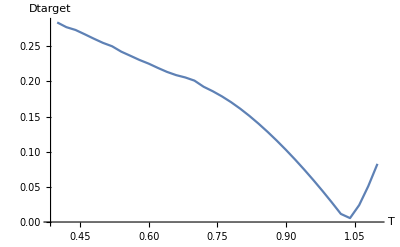

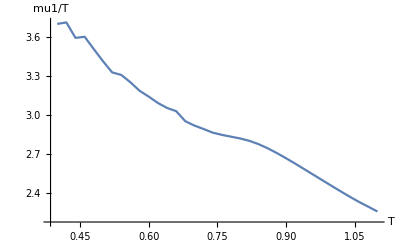

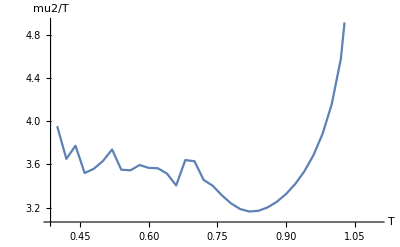

-Graphics3D-

```mathematica
ClearAll[e,mu,r,mu1,mu2,hFnc,zNeib,e0,mu0];
zNeib=4;
z2=(zNeib/2);
hFnc[r_, e_, mu_]:=mu.r + (r.e.r)*z2;
sFnc1[x_]:=x*Log[x];
sFnc[r_]:=Total[Table[sFnc1[x],{x,r}]] + sFnc1[1-Total[r]];
fFnc[r_, e_, mu_,t_]:=hFnc[r, e, mu]/t + sFnc[r];
fFncChi[r_, chi_, muChi_,t_]:=hFnc[r, chi/zNeib, muChi]/t + sFnc[{r[[2]], r[[3]]}];
eFromChi[chi0_]:={{chi0[[2]][[2]]-chi0[[1]][[2]]*2,chi0[[2]][[3]]-chi0[[1]][[2]]-chi0[[1]][[3]]},{chi0[[2]][[3]]-chi0[[1]][[2]]-chi0[[1]][[3]], chi0[[3]][[3]]-chi0[[1]][[3]]*2}}/zNeib;
phi12to012[phi_]:={1-phi[[1]]-phi[[2]],phi[[1]],phi[[2]]};
findMin[e_, mu_, t_,x0_,y0_]:=Module[{x,y},phi12to012[{x,y}/.FindMinimum[{fFnc[{x,y}, e, mu,t],{x>10^-6,y>10^-6,x+y<(1-10^-6)}},{{x,x0},{y,y0}}][[2]]]];
getMin0[e_, mu_, t_,phi0Tol_]:=findMin[e, mu, t,phi0Tol,phi0Tol];
getMin1[e_, mu_, t_,phi0Tol_]:=findMin[e, mu, t,1-phi0Tol,phi0Tol/2];
getMin2[e_, mu_, t_,phi0Tol_]:=findMin[e, mu, t,phi0Tol/2,1-phi0Tol];
getMins[e_, mu_, t_,phi0Tol_]:=
Module[{min0, min1, min2,nDists,d01,d02,d12},
min0=getMin0[e, mu, t,phi0Tol];
min1=getMin1[e, mu, t,phi0Tol];
min2=getMin2[e, mu, t,phi0Tol];
{min0, min1, min2}
];
nMins[e_, mu_, t_,phi0Tol_,phiEndTol_]:=Module[{min0, min1, min2,nDists,d01,d02,d12,mins},
mins = getMins[e, mu, t,phi0Tol];
d01 = Norm[mins[[1]]-mins[[2]]];
d02 = Norm[mins[[1]]-mins[[3]]];
d12 = Norm[mins[[3]]-mins[[2]]];
nDists = Boole[d01 > phiEndTol]+Boole[d02 > phiEndTol]+Boole[d12 > phiEndTol];
If[nDists==0,1,If[nDists==2,2,If[nDists==3,3,0]]]
];
distMu12[e_, mu_, t_,phi0Tol_]:=Norm[getMin0[e, mu, t,phi0Tol] - getMin1[e, mu, t,phi0Tol]];
costMu12[e_, mu_, t_,phi0Tol_, phiTarget0_, phiTarget1_]:=Module[{min0, min1},
min0=getMin0[e, mu, t,phi0Tol];
min1=getMin1[e, mu, t,phi0Tol];
Norm[phiTarget0 - min0]^2+Norm[phiTarget1 - min1]^2
];
optimizeTMu12[e_,tMax_,phi0Tol_, phiTarget0_, phiTarget1_]:=Module[{mu1,mu2,t,optRes},
optRes = NMinimize[{Hold[costMu12[e, {mu1, mu2}, t,phi0Tol, phiTarget0, phiTarget1]],mu1>0, mu1<10,mu2>0,mu2<10,t>0.1, t<tMax},{mu1, mu2, t}];
optParams={mu1,mu2,t}/.optRes[[2]];
optParams
];
optimizeMu12[e_, t_,phi0Tol_, phiTarget0_, phiTarget1_]:=Module[{mu1,mu2,optRes},
optRes = NMinimize[{Hold[costMu12[e, {mu1, mu2}, t,phi0Tol, phiTarget0, phiTarget1]],mu1>0, mu1<10,mu2>0,mu2<10},{mu1, mu2}];
optParams={mu1,mu2}/.optRes[[2]];
optParams
];

t0=1.25/2.68;
chi0 = {{0, 2.5,1.6},{2.5, 0, 1.6}, {1.6, 1.6, 0}};
muChi0 = {0, 0, 1.5};
(*t0=1.0;*)
tMax = 1.25 / 2.5;
phi0Tol=0.001;
phiEndTol=0.001;
(*e0 = {{-2.68, -1.34}, {-1.34,-1.715}};*)
e0 = eFromChi[chi0];mu0 = {muChi0[[2]]-z2*e0[[1]][[1]],muChi0[[3]] -z2*e0[[2]][[2]]};
mins0 = getMins[e0, mu0, t0,phi0Tol];
nMins0 = nMins[e0, mu0, t0,phi0Tol,phiEndTol];
phiTarget0 = phi12to012[{0.1863692, 0.008}];
phiTarget1 = phi12to012[{0.83606838, 0.008}];
cost0=costMu12[e0, mu0, t0,phi0Tol, phiTarget0, phiTarget1];

Print["t0 = ", t0];
Print["e0:", (e0)//MatrixForm];
Print["mu0:", mu0];
Print["mu_chi0:", mu0 +Diagonal[e0]*z2];
Print["e0/t0:", (e0/t0)//MatrixForm];
Print["mu0/t0:", mu0/t0];
Print["mu_chi0/t0:", (mu0 +Diagonal[e0]*z2)/t0];
Print["mins = ", mins0];
Print["nMins0 = ", nMins0];
Print["cost0 = ", Sqrt[cost0]];

tOpt=t0;
muOpt=mu0;
tOpt=1.0340372087826613;
muOpt={2.46576,5.24407};
tOpt=0.5;
muOpt={1.668267173733335,2.0065114310210634};

(*optTMu12 = optimizeTMu12[e0,tMax,phi0Tol, phiTarget0, phiTarget1];
muOpt={optTMu12[[1]], optTMu12[[2]]};
tOpt=optTMu12[[3]];*)
(*For the most-left Quiwei pair*)

costOpt=costMu12[e0, muOpt, tOpt,phi0Tol, phiTarget0, phiTarget1];
nMinsOpt = nMins[e0, muOpt, tOpt,phi0Tol,phiEndTol];
Print["tOpt:",tOpt];
Print["muOpt:",muOpt];
Print["muChiOpt:",muOpt + Diagonal[e0]*z2];
Print["e0/tOpt:", (e0/tOpt)//MatrixForm];
Print["muOpt/tOpt:", muOpt/tOpt];
Print["muChiOpt/tOpt:", (muOpt + Diagonal[e0]*z2)/tOpt];
Print["costOpt = ", Sqrt[costOpt]];
Print["nMinsOpt = ", nMinsOpt];

(*Compare H-chi vs. H-e*)
(*DensityPlot[fFncChi[{1-x-y,x,y}, chi0, muChi0,t0]-fFnc[{x,y}, e0, mu0,t0],{x,0,1},{y,0,1},RegionFunction->Function[{x,y},(x>0)&&(y>0)&&(x+y<1)],Frame->False,Axes->True,AxesLabel->{"c1", "c2"},PlotLegends->Automatic]*)

(*Local minimas position cs. T; Aka phase diagrams*)
(*Manipulate[ParametricPlot3D[{Join[getMin0[{{e11,e12},{e12,e22}}, {mu1,mu2}, 10^logT,phi0Tol],{10^logT}], Join[getMin1[{{e11,e12},{e12,e22}}, {mu1,mu2}, 10^logT,phi0Tol],{10^logT}],Join[getMin2[{{e11,e12},{e12,e22}}, {mu1,mu2}, 10^logT,phi0Tol],{10^logT}]},{logT,-0.7,0.2},PlotLegends->{"0", "1", "2"},AxesLabel->{"c1","c2","T"}],{{e11,e0[[1]][[1]]},-5,0}, {{e12,e0[[1]][[2]]},-5,0},{{e22,e0[[2]][[2]]},-5,0}, {{mu1,muOpt[[1]]},0,10},{{mu2,muOpt[[2]]},0,10}]
Manipulate[ParametricPlot[{getMin0[{{e11,e12},{e12,e22}}, {mu1,mu2}, 10^logT,phi0Tol], getMin1[{{e11,e12},{e12,e22}}, {mu1,mu2}, 10^logT,phi0Tol],getMin2[{{e11,e12},{e12,e22}}, {mu1,mu2}, 10^logT,phi0Tol]},{logT,-0.7,0.2},PlotLegends->{"0", "1", "2"},AxesLabel->{"c1","c2"}],{{e11,e0[[1]][[1]]},-5,0}, {{e12,e0[[1]][[2]]},-5,0},{{e22,e0[[2]][[2]]},-5,0}, {{mu1,muOpt[[1]]},0,10},{{mu2,muOpt[[2]]},0,10}]*)

(*muOptData =Parallelize[Table[{t,optimizeMu12[e0, t,phi0Tol, phiTarget0, phiTarget1]},{t,0.4,1.1,0.02}],ProgressReporting->True,Method->"FinestGrained"];*)
distData = Table[{mus[[1]], Sqrt[costMu12[e0, mus[[2]], mus[[1]],phi0Tol, phiTarget0, phiTarget1]]},{mus, muOptData}];
ListLinePlot[distData,AxesLabel->{"T","Dtarget", "f/T"}]
ListLinePlot[Table[{ mus[[1]],mus[[2]][[1]]/mus[[1]]},{mus, muOptData}],AxesLabel->{"T","mu1/T"}]
ListLinePlot[Table[{ mus[[1]],mus[[2]][[2]]/mus[[1]]},{mus, muOptData}],AxesLabel->{"T","mu2/T"}]
ListLinePlot3D[Table[{mus[[2]][[1]]/mus[[1]],mus[[2]][[2]]/mus[[1]], mus[[1]]},{mus, muOptData}],AxesLabel->{"mu1/T","mu2/T", "T"}]

(*Grand free energy 3D profile*)
Manipulate[Module[{tLocal, eLocal,muLocal, phi0Local, phi1Local},
tLocal=10^logT;
eLocal={{e11,e12},{e12,e22}};
muLocal={mu1,mu2};
phi0Local = getMin0[eLocal, muLocal, tLocal,phi0Tol];
phi1Local = getMin1[eLocal, muLocal, tLocal,phi0Tol];
Plot3D[fFnc[{x,y}, eLocal, muLocal,tLocal],{x,0,1},{y,0,1},RegionFunction->Function[{x,y},(x>0)&&(y>0)&&(x+y<1)],ColorFunction->Function[{x,y,z},Hue[(1-z)*0.65]],AxesLabel->{"c1","c2", "f/T"},PlotLabel->("mins:" <> ToString[phi0Local] <>ToString[phi1Local] )]],{{e11,e0[[1]][[1]]},-5,0}, {{e12,e0[[1]][[2]]},-5,0},{{e22,e0[[2]][[2]]},-5,0}, {{mu1,muOpt[[1]]},0,10},{{mu2,muOpt[[2]]},0,10}, {{logT,Log[tOpt]/Log[10]},-1,1}]

(*Grand free energy heat map*)Manipulate[DensityPlot[fFnc[{x,y}, {{e11,e12},{e12,e22}}, {mu1,mu2},10^logT],{x,0,1},{y,0,1},RegionFunction->Function[{x,y},(x>0)&&(y>0)&&(x+y<1)],Frame->False,Axes->True,AxesLabel->{"c1", "c2"},PlotLegends->Automatic],{{e11,e0[[1]][[1]]},-5,0}, {{e12,e0[[1]][[2]]},-5,0},{{e22,e0[[2]][[2]]},-5,0}, {{mu1,muOpt[[1]]},0,10},{{mu2,muOpt[[2]]},0,10},{{logT,Log[tOpt]/Log[10]},-1,1}]

(*Number of local minimas*)(*nMinData = Table[{mu1, mu2, nMins[e0, {mu1,mu2}, tOpt,phi0Tol,phiEndTol]},{mu1,muOpt[[1]]-0.1,muOpt[[1]]+0.1,0.01},{mu2,2,10,0.1}];
ListPointPlot3D[nMinData,ColorFunction->"Rainbow"]*)
(*Plot[nMins[e0, muOpt, 10^logT,phi0Tol,phiEndTol],{logT,-1,1}]
Manipulate[
Module[{muOptLocal,optMu12Local,e0Local,muRanges},
e0Local={{e11,e12},{e12,e22}};
optMu12Local = optimizeMu12[e0Local,t,phi0Tol, phiTarget0, phiTarget1];
muOptLocal={optMu12Local[[1]], optMu12Local[[2]]};
Print["tOptLocal = ",t];
muRanges = {{muOptLocal[[1]]-0.2,muOptLocal[[1]]+0.2},{muOptLocal[[2]]-0.2,muOptLocal[[2]]+0.2}}/t;
DensityPlot[nMins[e0Local, {mu1,mu2}*t, t,phi0Tol,phiEndTol],{mu1,muRanges[[1]][[1]],muRanges[[1]][[2]]},{mu2,muRanges[[2]][[1]],muRanges[[2]][[2]]},Frame->False,Axes->True,AxesLabel->{"mu1/T", "mu2/T"},PlotLegends->Automatic,PlotPoints->Round[Max[{muRanges[[1]][[2]]-muRanges[[1]][[1]],muRanges[[2]][[2]]-muRanges[[2]][[1]]}]/0.1]]],
{{e11,e0[[1]][[1]]},-5,0}, {{e12,e0[[1]][[2]]},-5,0},{{e22,e0[[2]][[2]]},-5,0},{{t,tOpt},0.1,10}]*)
```

2 False+True

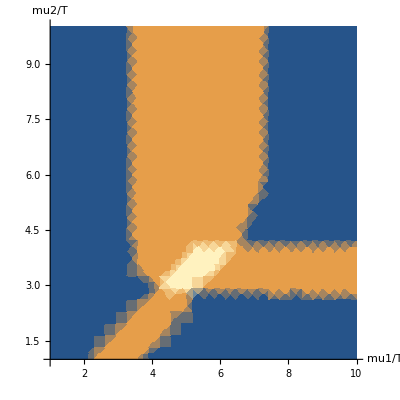

```mathematica
(1>0)+(2>3)+(1<0)
Boole[]
```

```mathematica
Log10[1.0340372087826613]
```

Join::heads: Heads getMin0 and List at positions 1 and 2 are expected to be the same.

Join::heads: Heads getMin1 and List at positions 1 and 2 are expected to be the same.

Join::heads: Heads getMin2 and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Join::heads: Heads getMin0 and List at positions 1 and 2 are expected to be the same.

Join::heads: Heads getMin1 and List at positions 1 and 2 are expected to be the same.

Join::heads: Heads getMin2 and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Join::heads: Heads getMin0 and List at positions 1 and 2 are expected to be the same.

Join::heads: Heads getMin1 and List at positions 1 and 2 are expected to be the same.

Join::heads: Heads getMin2 and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
tOpt1=1.0340372087826613;(*{x,2,3},{y,3,6}*)
tOpt1=0.8;(*{x,2, 4},{y,2,6}*)
tOpt1=0.4;
(*muOpt1 = {2.46576,5.24407};
Print["muOpt = ", muOpt1];
nMins[e0, muOpt1, tOpt1,phi0Tol,phiEndTol]*)
(*Plot3D[nMins[e0, {x,y}, tOpt,phi0Tol,phiEndTol],{x,1,10},{y,1,10},AxesLabel->{"mu1", "mu2", "nMins"}]*)
(*DensityPlot[nMins[e0, {x,y}, tOpt,phi0Tol,phiEndTol],{x,muOpt[[1]]-0.2,muOpt[[1]]+0.2},{y,muOpt[[2]]-0.2,muOpt[[2]]+0.2},Frame->False,Axes->True,AxesLabel->{"mu1", "mu2"},PlotLegends->Automatic]*)
(*ListPointPlot3D[Table[{mu1, mu2, nMins[e0, {mu1,mu2}, tOpt,phi0Tol,phiEndTol]},{mu1,1,10,0.5},{mu2,1,10,0.5}],ColorFunction->"Rainbow"]*)
dataRaw2D = Table[{x,y, distMu12[e0, {x,y}*tOpt1, tOpt1,phi0Tol]},{x, 4, 5,0.5},{y, 4, 5,0.5}];
data2D=Flatten[dataRaw2D,1];
ListDensityPlot[data2D,Frame->False,Axes->True,AxesLabel->{"mu1/T", "mu2/T"},PlotLegends->Automatic]
(*DensityPlot[distMu12[e0, {x,y}*tOpt1, tOpt1,phi0Tol],{x,4,5.0},{y,4,5},Frame->False,Axes->True,AxesLabel->{"mu1/T", "mu2/T"},PlotLegends->Automatic,PlotPoints->Round[(1)/0.05]]*)
(*DensityPlot[nMins[e0, {x,y}*tOpt1, tOpt1,phi0Tol,phiEndTol],{x,2.8, 3.5},{y,3,6},Frame->False,Axes->True,AxesLabel->{"mu1/T", "mu2/T"},PlotLegends->Automatic,PlotPoints->Round[(0.7)/0.02]]*)
```

-Graphics-

```mathematica
(*muOptT = optimizeMu12[e0,0.44,phi0Tol, phiTarget0, phiTarget1]*)
costT=costMu12[e0, muOptT, 0.44,phi0Tol, phiTarget0, phiTarget1];
Print["costT = ",Sqrt[costT]];
```

costT = 0.199574

```mathematica
(*{x, 2, 8, 0.1},{y, 2.5, 5, 0.1},{t, 0.4, 1.1, 0.1}*)
(*{x, 2, 4, 0.1},{y, 2, 6, 0.1},{t, 0.4, 1.1, 0.1}*)
(*{x, 2, 4, 0.5},{y, 2, 6, 0.5},{t, 0.4, 1.1, 0.5}*)(*for tests*)
data3D=Flatten[Table[{x,y,t, distMu12[e0, {x,y}*t, t,phi0Tol]},{x, 2, 8, 0.1},{y, 2, 5, 0.1},{t, 0.4, 1.3, 0.02}],2];
cData = Table[{d[[4]]},{d,data3D}];
dataRange = Max[cData] - Min[cData];
ListDensityPlot3D[data3D,Axes->True,AxesLabel->{"mu1/T", "mu2/T","T"},PlotLegends->Automatic]
ListDensityPlot3D[data3D,Axes->True,AxesLabel->{"mu1/T", "mu2/T","T"},PlotLegends->Automatic,OpacityFunction->(((#-Min[cData])/dataRange/3)&),OpacityFunctionScaling->False]
(*DensityPlot3D[distMu12[e0, {x,y}*t, t,phi0Tol],{x,2, 4},{y,2,6},{t,0.4,1.05},Axes->True,AxesLabel->{"mu1/T", "mu2/T","T"},PlotLegends->Automatic,PlotPoints->{20,30,10}]*)
```

-Graphics3D-

-Graphics3D-

```mathematica
cData = Table[{d[[4]]},{d,data3D}];
range = Max[cData] - Min[cData];
Manipulate[ListDensityPlot3D[Table[{d[[1]],d[[2]],d[[3]],Boole[(d[[4]]>cMin)&&(d[[4]]<cMax)]},{d,data3D}],Axes->True,AxesLabel->{"mu1/T", "mu2/T","T"},PlotLegends->Automatic,OpacityFunction->((#/2)&),OpacityFunctionScaling->False],{{cMin,Max[Norm[phiTarget0-phiTarget1]-0.2,0]},0,Sqrt[2]},{{cMax,Min[Norm[phiTarget0-phiTarget1]+0.2, Sqrt[2]]},0,Sqrt[2]}]
```

Table::iterb: Iterator {d,data3D} does not have appropriate bounds.

Table::nliter: Non-list iterator VectorQ[{d,data3D}] at position 2 does not evaluate to a real numeric value.

ListDensityPlot3D::ldata: Table[{d⟦1⟧,d⟦2⟧,d⟦3⟧,Boole[d⟦4⟧>FE`cMin$$43&&d⟦4⟧<FE`cMax$$43]},{d,data3D}] is not a valid dataset or list of datasets.

```mathematica
1
```

-Graphics3D-

-Graphics3D-

1

```mathematica
Norm[phiTarget0-phiTarget1]
```

0.918813